# Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252
scientific contributors: Fernando, Simon

Recent Silicon device inspired by the Delft

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

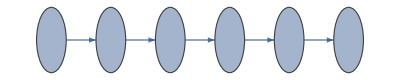

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->7.,1->8.413984696401544,2->5.102844267367531,3->7.552239500777061,4->3.3081835637502737,5->4.29844012820983|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,

(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,

(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9526707113340579,1->0.9395929490898237,2->0.9484194291327452,3->0.9850519102118337,4->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2
*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10,
RepeatRead->2
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Tests

```mathematica
ψ=CreateQureg[6];
ρ=CreateDensityQureg[6];
```

Remarks: the time unit is μs

### Passive noise

The passive noise when no gates are applied.
The noise forms:
1) Cross-talk C_i[Rz_(i+1)(Δt)]  from input ExchangeRotOff, which is exchange rotation when no C[Z] gate is applied. 
2) Standard dephasing from T2 or T2* input and depolarising from T1 inputs.
3) If dynamical decoupling is active, DDActive->True, then T2 information is used, otherwise T2s information used. 

The standard passivenoise (2) can be eliminated by setting StdPassiveNoise -> False. The Cross-talk (1) can be set off by setting ExchangeRotOff->False

{{0,{Deph_0[0.100502],Depol_0[0.0000235616]},{Deph_0[0.],Depol_0[0.],Deph_1[0.0691683],Depol_1[0.0000235616],Deph_2[0.0376768],Depol_2[0.0000235616],Deph_3[0.0404918],Depol_3[0.0000235616],Deph_4[0.0339344],Depol_4[0.0000235616],Deph_5[0.055502],Depol_5[0.0000235616]}}}

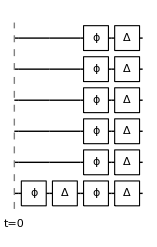

```mathematica
InsertCircuitNoise[{Subscript[Wait, 0][π]},SiliconDelft[ExchangeRotOff->False]]
DrawCircuit[%]
```

### Single qubit gates

Single qubit gates: x- and y- rotations have the same error 
The noise forms:
1) Off-resonant Rabi Oscillation. This takes RabiFreq input and applied when OffResonantRabi->True.
2) Standard Dephasing and Depolarising noise. This takes FidSingleXY and EFSingleXY inputs to estimate the error parameters. Set EFSingleXY->{0,0} to set this off.

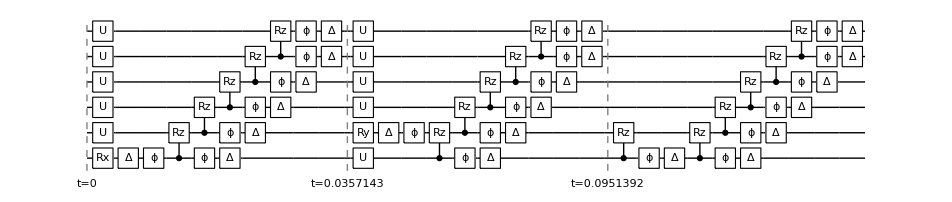

```mathematica
GetNoisyForm[{Subscript[Rx, 0][π/2],Subscript[Ry, 1][π],Subscript[Wait, 0][1]},SiliconDelft[StdPassiveNoise->True,OffResonantRabi->True],Parallel->None];
DrawCircuit[%]
```

```mathematica
Options@SiliconDelft
```

{qubitsNum→6,T1→100000,T2s→<|0→3,1→2.5,2→3.7,3→3.7,4→5.9,5→5.1|>,T2→<|0→14,1→21.1,2→40.1,3→37.2,4→44.7,5→26.7|>,DDActive→True,QubitFreq→<|0→15620.,1→15880.,2→16300.,3→16100.,4→15900.,5→15690.|>,RabiFreq→<|0→7.,1→8.41398,2→5.10284,3→7.55224,4→3.30818,5→4.29844|>,OffResonantRabi→True,StdPassiveNoise→True,FidSingleXY→<|0→0.9977,1→0.9987,2→0.9996,3→0.9988,4→0.9991,5→0.9989|>,EFSingleXY→{0,1},FreqCZ→<|0→12.1,1→11.1,2→6.6,3→9.8,4→5.4|>,FidCZ→<|0→0.952671,1→0.939593,2→0.948419,3→0.985052,4→0.966317|>,EFCZ→{0,1},ExchangeRotOn→{{0,0.023,0.018,0.03,0.04},{0.05,0,0.03,0.03,0.04},{0.05,0.03,0,0.07,0.042},{0.038,0.03,0.031,0,0.25},{0.033,0.03,0.02,0.03,0}},ExchangeRotOff→<|0→0.039,1→0.015,2→0.03,3→0.02,4→0.028|>,FidRead→0.99,DurRead→10,RepeatRead→2}

Controlled-Z

The noise forms:
1) Standard 2-qubits dephasing and depolarising noise. This takes information FidCZ (fidelities) and EFCZ (error fraction). Set it off by EFCZ->{0,0}
2) Exchange rotation when C-Z is on. Takes information ExchangeRotOn. Set ExchangeRotOn -> False to set it off.

{{0,{C_0[Z_1],Depol_(0,1)[0],Deph_(0,1)[0],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]]},{Deph_0[0.],Depol_0[0.],Deph_1[0.],Depol_1[0.],Deph_2[0.000514975],Depol_2[3.09917×10^-7],Deph_3[0.000555099],Depol_3[3.09917×10^-7],Deph_4[0.000462005],Depol_4[3.09917×10^-7],Deph_5[0.000773228],Depol_5[3.09917×10^-7]}}}

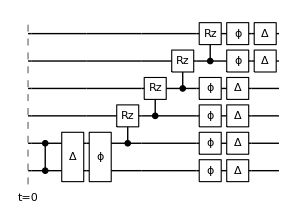

```mathematica
GetNoisyForm[{Subscript[C, 0][Subscript[Z, 1]]},SiliconDelft[StdPassiveNoise->True,EFCZ->{0,0}]]
DrawCircuit[%]
```

## Reproducing results from the paper

Initialisation is obtained by 2 readouts and a partial swap with single qubit errors
The qubits are initialised to state 100 ... 001

### Initialisation fidelity goal: 0.95 (quoted value)

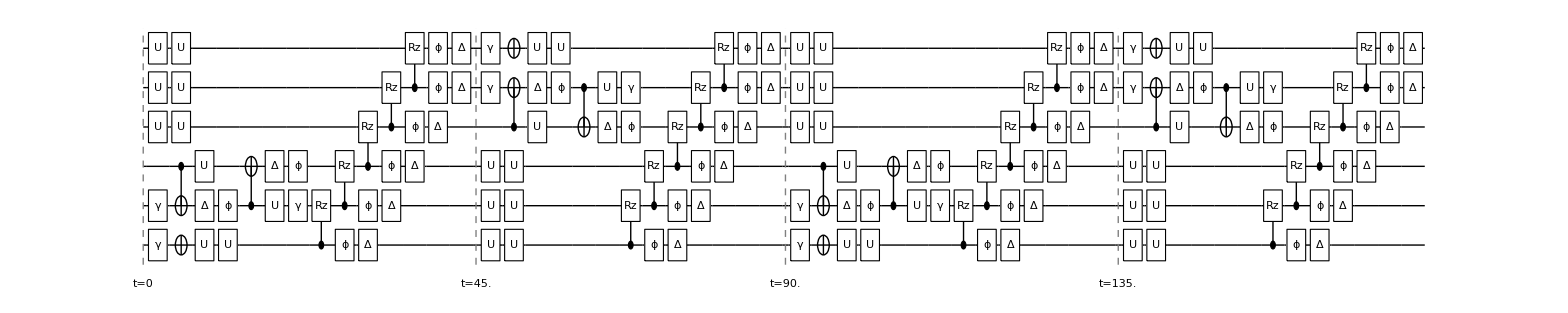

0.958825

```mathematica
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
noisycirc=GetNoisyForm[{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[Init, 0,1,2],Subscript[Init, 3,4,5]},SiliconDelft[RabiFreq->Association[#->5&/@Range[0,5]]]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[X, 5]}];
CalcFidelity[ρ,ψ]
```

### Obtaining T_2 : X90 - tau - X180 - tau - X90, tau = 1 μs

```mathematica
HahnEchoExperiment[dev_,qubit_]:=Module[{init},
If[MemberQ[{0,1,2},qubit],init=Subscript[Init, 0,1,2]];
If[MemberQ[{3,4,5},qubit],init=Subscript[Init, 3,4,5]];
Table[
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@GetNoisyForm[{init,Subscript[Rx, qubit][π/2],Subscript[Wait, 0][t],Subscript[Rx, qubit][π],Subscript[Wait, 0][t],Subscript[Rx, qubit][π/2]},dev]];
{t,CalcProbOfOutcome[ρ,qubit,If[MemberQ[{5,0},qubit],1,0]]},{t,0,30,3}]
]
```

```mathematica
OptionValue[SiliconDelft,T2]
```

<|0→14,1→21.1,2→40.1,3→37.2,4→44.7,5→26.7|>

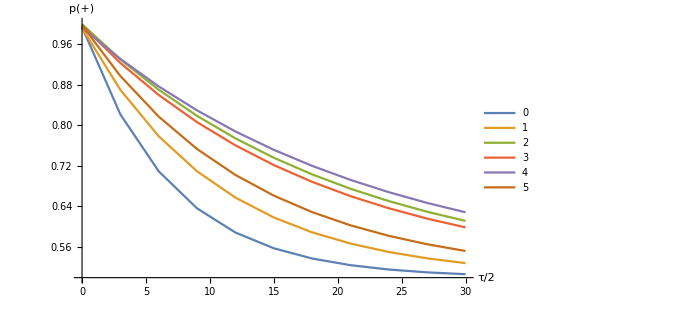

```mathematica
ListPlot[HahnEchoExperiment[SiliconDelft[DDActive->True],#]&/@Range[0,5],PlotLegends->Range[0,5],PlotRange->{0.5,1},Joined->True,ImageSize->500,AxesLabel->{"τ/2","p(+)"}]
```

ideal plot to the Total wait time t/2
Plot[(1+ⅇ^(-x/#))/2&/@Values@OptionValue[SiliconDelft,T2],{x,0,60},PlotRange→{0.5,1},ImageSize→500]

### Bell states

The CZ gates’ fidelities are unknown. We set it according to the results on the Bell states fidelity.

```mathematica
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
```

```mathematica
chartstyle={ImageSize->200,BarSpacing->0.01,ChartBaseStyle->EdgeForm[{Thick,Black}],ColorFunction->Function[{height},ColorData["Rainbow"][height*10]]};
```

```mathematica
concurence[ρ_]:=Module[{eigv,ρm,ρms,ρt,nq,pauliy},
ρm=GetQuregMatrix@ρ;
nq=IntegerPart@Log2@Length@ρm;
ρms=MatrixPower[ρm,1/2];
pauliy=CalcCircuitMatrix[Subscript[Y, #]&/@Range[0,nq-1]];
ρt=pauliy.Conjugate[ρm].pauliy;
eigv=Reverse@Sort[Chop@Eigenvalues[MatrixPower[ρms.ρt.ρms,1/2]]];
Max[0,eigv[[1]]-Total@eigv[[2;;]]]
]
```

```mathematica
bellcircρ=<|"01"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]},"23"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][π/2]},"34"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2]},"45"->{Subscript[Rx, 4][π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}|>;
bellcircψ=<|"01"->{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"23"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"34"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"45"->{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]}|>;
```

```mathematica
bell[code_,dev_]:=Module[{init={},qubits,fid,plot,conc,str},
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,{Subscript[Init, 0,1,2],Subscript[Init, 0,1,2]}]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,{Subscript[Init, 3,4,5],Subscript[Init, 3,4,5]}]];

SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@GetNoisyForm[{init,bellcircρ[code]},dev]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
conc=concurence[ρ2];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
fid=CalcFidelity[ρ2,ψ2]*100;
plot=PlotDensityMatrix[ρ2,ψ2,Sequence@@chartstyle];
str="("<>StringRiffle[qubits+1,"-"]<>")";
{plot,"F"<>str<>"="<>ToString@fid,"conc="<>ToString[100*conc]}
]
```

-Graphics-

```mathematica
Grid@Transpose[bell[#,SiliconDelft[EFSingleXY->{1,0}]]&/@ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
F(1-2)=89.2001 | F(2-3)=91.828 | F(3-4)=88.2639 | F(4-5)=96.7676 | F(5-6)=94.746
conc=86.7178 | conc=83.7498 | conc=85.5062 | conc=94.7692 | conc=90.6208

### 3 - qubits GHZ

```mathematica
ψ3=CreateQureg[3];
ρ3=CreateDensityQureg[3];
```

```mathematica
ghzcircρ=<|
"012"->{Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},"123"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2]},
"234"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][-π/2]},
"345"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][-π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}
|>;
ghzcircψ=<|
"012"->Join[{Subscript[X, 0]},ghzcircρ["012"]],
"123"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"234"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"345"->{Subscript[X, 2],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]}
|>;

ghz[code_,dev_]:=Module[{init={},qubits,fid,plot},
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@GetNoisyForm[{init,ghzcircρ[code]},dev]];
SetQuregMatrix[ρ3,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ3,ghzcircψ[code]];
fid=100*CalcFidelity[ρ3,ψ3]*Times@@(OptionValue[SiliconDelft,FidSingleXY][#]&/@qubits)*OptionValue[SiliconDelft,FidRead]^3;
plot=PlotDensityMatrix[ρ3,ψ3,Sequence@@chartstyle];
{plot,"F_est("<>StringRiffle[qubits+1,"-"]<>")="<>ToString@fid}
]
```

-Graphics-

```mathematica
Grid@Transpose[ghz[#,SiliconDelft[]]&/@ReplaceList[Sort@Range[0,5],{p___,a_,b_,c_,q___}:>StringRiffle[{a,b,c},""]]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
F_est(1-2-3)=76.4544 | F_est(2-3-4)=81.7172 | F_est(3-4-5)=79.8137 | F_est(4-5-6)=86.1358